## 4N

Calke mozna interpretowac jako pole powierzchni pod wykresem funkcji podcalkowej.

```mathematica
f[t_]:=Cos[(1+t)/(t^2+0.04)] ⅇ^(-t^2);
```

```mathematica
Needs["Graphics`FilledPlot`"];
```

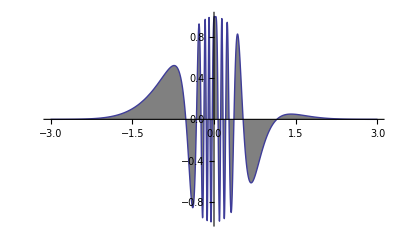

```mathematica
FilledPlot[f[t],{t,-3,3},PlotRange->Full]
```

Obliczanie granicy lim_(x→∞) F(x)=∫_(-∞)^x Cos[(1+t)/(t^2+0.04)]ⅇ^(-t^2)ⅆt
∑_(k=1)^(m-1) f[X_(2k)]+4∑_(k=1)^m f[X_(2k-1)]

```mathematica
f[t_]:=Cos[(1+t)/(t^2+0.04)] ⅇ^(-t^2);
```

```mathematica
Simpson[aa_,bb_,m_]:=
Module[{a=N[aa],mm=m,b=N[bb],k,,X},
Return[ (b-a)/6(f[a]+f[b]+4f[(a+b)/2]) ]; ];
```

```mathematica
ka[a_,b_,err_]:=Module[{c},
c=(a+b)/2; 
ab=Simpson[a,b,err]; 
ac=Simpson[a,c,err]; 
cb=Simpson[c,b,err]; 
If[ Abs[ab-ac-cb]<err,
Return[ ac+cb ],
Return[ka[a,c,err/2]+ka[c,b,err/2]]]; ]
 
Print["Wynik: Lim_(x → ∞)F(x)=", ka[-20,20.0,0.00000001]];
```

Wynik: Lim_(x → ∞)F(x)=0.219612